{{a→InterpolatingFunction[{{0., 30.}}, <>]}}

Evolution of the Scale Factor:

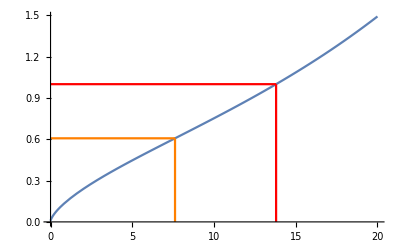

Evolution of the Hubble Parameter:

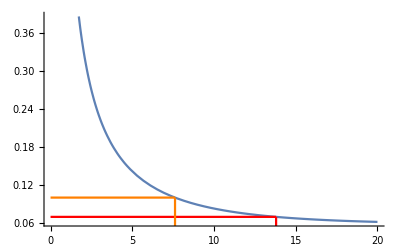

Evolution of the Particle Horizon:

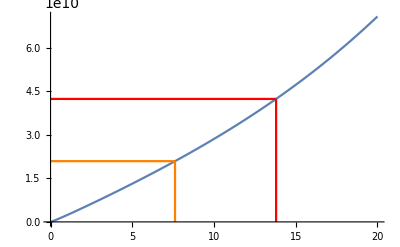

Evolution of the Event Horizon:

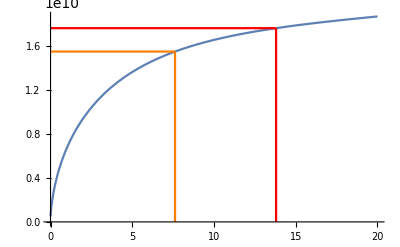

```mathematica
c=Rationalize[10^9];
H0=Rationalize[0.06923];
Ωm=Rationalize[0.3089];
Ωr=Rationalize[0.0000];
Ωk=Rationalize[0.0000];
ΩΛ=Rationalize[0.6911];
t0=Rationalize[13.799];
p0=Rationalize[4.24073*10^10];
e0=Rationalize[1.76080*10^10];
tΛ=Rationalize[7.61595];
aΛ=Rationalize[0.60696];
HΛ=Rationalize[0.09967];
pΛ=Rationalize[2.09451*10^10];
eΛ=Rationalize[1.54817*10^10];
time=20;
Epoch[a_,t_,col_]:=ListLinePlot[{{{0,a},{t,a}},{{t,0},{t,a}}},PlotStyle->col];
H[t_]:=H0*Sqrt[Ωm/a[t]^3+Ωr/a[t]^4+Ωk/a[t]^2+ΩΛ];
sol=NDSolve[{a'[t]/a[t]==H[t],a[t0]==1},a,{t,0,3time/2}]
"Evolution of the Scale Factor:"
Show[Plot[a[t]/.sol,{t,0,time}],Epoch[1,t0,Red],Epoch[aΛ,tΛ,Orange]]
"Evolution of the Hubble Parameter:"
Show[Plot[H[t]/.sol,{t,0,time}],Epoch[H0,t0,Red],Epoch[HΛ,tΛ,Orange]]
"Evolution of the Particle Horizon:"
Show[Plot[(a[t]/.sol)NIntegrate[c/a[𝓉]/.sol,{𝓉,0,t}],{t,0,time}],Epoch[p0,t0,Red],Epoch[pΛ,tΛ,Orange]]
"Evolution of the Event Horizon:"
Show[Plot[(a[t]/.sol)NIntegrate[c/a[𝓉]/.sol,{𝓉,t,100time}],{t,0,time}],Epoch[e0,t0,Red],Epoch[eΛ,tΛ,Orange]]
```